# ARPES best fit model for the surface bands of Sr_2 RuO_4

Anirudh Chandrasekaran

Loughborough University
11 June 2024

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Sr2RuO4"]<>"Package"];
<<BandUtilities`
```

## Interpolating between the Wannier90 files

### Ingredients needed for symmetrization

```mathematica
ρ={{0,-1,0},{1,0,0},{0,0,1}}; (*The matrix part of the Subscript[C, 4] rotation about one of the Ru atoms.*)
Uρ={{0,-1,0},{1,0,0},{0,0,-1}}; (*Representation of Subscript[C, 4] rotation in the d-orbital space.*)

rxy={{0,1,0},{1,0,0},{0,0,1}};  (*x<->y reflection.*)
Urxy={{-1,0,0},{0,1,0},{0,0,-1}}; (*Representation of the x<->y reflection.*)

c0={1/4,3/4,0}; (*Location of one of the Ru atoms, which we shall use as the centre of the Subscript[C, 4] rotation.*)

AtomLocations={{3/4,1/4,0},{3/4,1/4,0},{3/4,1/4,0},{1/4,3/4,0},{1/4,3/4,0},{1/4,3/4,0}}; (*Location of the basis atoms in the fractional coordinates within the unit cell.*)

SymmetryList={}; (*This is a multidimensional list which we shall construct below. Each element is a sublist corresponding to a particular symmetry. First element of the sublist is real space symmetry's matrix part, second element is the translation part and the third element is its representation in the Hilbert space. Our point group is Subscript[D, 4], or Subscript[D, 8] in some pepole's notation.*)
Do[
AppendTo[SymmetryList,{MatrixPower[ρ,i],(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]]}];

AppendTo[SymmetryList,{MatrixPower[ρ,i].rxy,(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]].ArrayFlatten[{{0,1},{1,0}}⊗Urxy]}];
,{i,1,4}];
```

### Interpolation with symmetrization

We now interpolate between the Wannier90 data for 13 different rotations of the RuO octahedra: 0° through 12° to generate a continuously θ dependent Hamiltonian, whilst ensuring that the interpolated model has the right symmetry (for which we are feeding the list SymmetryList):

```mathematica
FileLocn=NotebookDirectory[]<>"unrenormalized2/";

W90Data=LoadInterpolateTBMs[{FileLocn<>"Sr2RuO4_0deg.dat",FileLocn<>"Sr2RuO4_1deg.dat",FileLocn<>"Sr2RuO4_2deg.dat",FileLocn<>"Sr2RuO4_3deg.dat",FileLocn<>"Sr2RuO4_4deg.dat",FileLocn<>"Sr2RuO4_5deg.dat",FileLocn<>"Sr2RuO4_6deg.dat",FileLocn<>"Sr2RuO4_7deg.dat",FileLocn<>"Sr2RuO4_8deg.dat",FileLocn<>"Sr2RuO4_9deg.dat",FileLocn<>"Sr2RuO4_10deg.dat",FileLocn<>"Sr2RuO4_11deg.dat",FileLocn<>"Sr2RuO4_12deg.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"Symmetries"->SymmetryList,"OrbitalCentres"->AtomLocations,"ParameterSymbol"->"θ"];

Hamltn1[k1_,k2_,θ_]=W90Data[[1]];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 6

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {741,853,853,853,845,853,853,853,853,853,853,853,853}

Interpolating between the Hamiltonians.

Valid symmetrization scheme provided! We will symmetrize the loaded Hamiltonian.

Number of supercells after symmetrization: 79

## Phenomenological spin orbit term

We now construct the phenomenological SOC terms:

```mathematica
Lx={{0,0,ⅈ},{0,0,0},{-ⅈ,0,0}};
Ly={{0,0,0},{0,0,ⅈ},{0,-ⅈ,0}};
Lz={{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}};

Hupup=1/2 Lz;
Hupdown=1/2(Lx+ⅈ Ly); 
Hdownup=1/2(Lx-ⅈ Ly);
Hdowndown=-1/2 Lz;
Zero2=ConstantArray[0,{3,3}];


HSOC=Join[Join[Hupup,Zero2,Hupdown,Zero2,2],Join[Zero2,Hupup,Zero2,Hupdown,2],Join[Hdownup,Zero2,Hdowndown,Zero2,2],Join[Zero2,Hdownup,Zero2,Hdowndown,2]];
```

## Reconstructing the full interpolated Hamiltonian

The full Hamiltonian incorporating SOC with tunable SOC strength and tunable θ. A version for the √2×√2 unit cell that is tailor made for fitting to the ARPES data is also defined (since the bulk has one Ru atom per unit cell, its Brillouin zone has twice the area of the default surface band BZ, which is also ‘rotated’ by 45°).

```mathematica
Hamiltonian[k1_,k2_,θ_,λ_]=0.5(ArrayFlatten[IdentityMatrix[2]⊗Hamltn1[k1,k2,θ]]+λ HSOC+ComplexExpand[ConjugateTranspose[ArrayFlatten[IdentityMatrix[2]⊗Hamltn1[k1,k2,θ]]+λ HSOC]]);
```

We can check the eigenvalues at a high symmetry point to see if the symmetrisation was successful, and has eliminated the weak splitting of degeneracies at the high symmetry points

```mathematica
NumberForm[Sort[Eigenvalues[Hamiltonian[π,-π,8,0.175]//N]],10]
```

{-0.5770901494,-0.5770901494,-0.5770901494,-0.5770901494,-0.0829819119,-0.0829819119,-0.0829819119,-0.0829819119,0.3197870614,0.3197870614,0.3197870614,0.3197870614}

For the sake of plotting, series expansion etc, we define the following compact versions, which are also recast in terms of the bulk band Brillouin zone using the transformation (k_x,k_y)->(k_x-k_y,k_x+k_y). This is needed since the bulk band real space unit cell is smaller by a factor of 2 (in area) and lattice vectors are also π/4 rad rotated from the surface unit cell.

```mathematica
HamSOC[k_]:=Hamiltonian[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],k[[4]]]

HamNoSOC[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]]]

HamSOCmeV[k_]:=1000Hamiltonian[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],k[[4]]]

HamNoSOCmeV[k_]:=1000Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]]]
```

## Evolution of the band structure with θ

We are now in a position to visualise the evolution of the band structure as θ is varied. But we first define some parameters needed for plotting, including the path in k-space

```mathematica
HSymmPts={{{0,0},"Γ"},{{π/2,π/2},"X"},{{0,π},"M"},{{0,0},"Γ"}};
HSymmPtsNoLabel={{{0,0},""},{{π/2,π/2},""},{{0,π},""},{{0,0},""}};
AngleList={0,3,6,9,12};

OpacityList={0.1,0.2,0.35,0.5,1};
ColourChoice={67/255,49/255,12/255}; (*This for one choice of colour scheme - with a fixed colour and varying transparency given by the alpha channel.*)

λSOC=0.175;
```

We now generate the band-structure data for the angles in the list using our routine which can also handle piecewise continuous k-paths (kindly have patience!! Mathematica can be a bit slow sometimes 🙁):

```mathematica
BandDataList=First@Last@Reap[Do[
HamCurr[k_]:=Hamiltonian[k[[1]]-k[[2]],k[[1]]+k[[2]],angle,λSOC];

Sow[GenerateBandStructure[HamCurr,HSymmPts,"TotalPoints"->500]];
,{angle,AngleList}]];
```

We will use our custom-built routine for plotting the band-structure as well:

```mathematica
BandPlotList=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList[[i]],{-1,1}(*meV range*),"AspectRatio"->3/4,"yLabel"->{ "E (eV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Helvetica"},"xLabel"->{12,Black,"Helvetica"},"yTicks"->{9,Black,"Helvetica"},"LineThickness"->0.003,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"DividingLines"->{(*Dashing[..]*)0.02,(*Color*)Gray,(*Thickness*)0.005},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Helvetica"],Scaled[{0.62,1.01-i/20.}]}]];
,{i,1,Length[AngleList]}]];
```

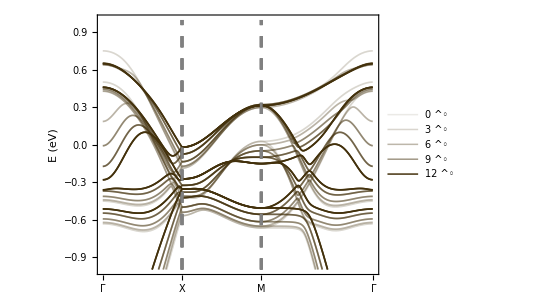

```mathematica
SpaghettiPlot=Show[BandPlotList,ImageSize->Full]
```

The data used to generate the figure can be saved so that it can also be plotted with other utilities like Gnuplot.

```mathematica
Export[NotebookDirectory[]<>"Figures/data/Theta_0.dat",BandDataList[[1,1]]]
Export[NotebookDirectory[]<>"Figures/data/Theta_3.dat",BandDataList[[2,1]]]
Export[NotebookDirectory[]<>"Figures/data/Theta_6.dat",BandDataList[[3,1]]]
Export[NotebookDirectory[]<>"Figures/data/Theta_9.dat",BandDataList[[4,1]]]
Export[NotebookDirectory[]<>"Figures/data/Theta_12.dat",BandDataList[[5,1]]]
```

/Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/Figures/data/Theta_0.dat

/Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/Figures/data/Theta_3.dat

/Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/Figures/data/Theta_6.dat

/Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/Figures/data/Theta_9.dat

/Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/Figures/data/Theta_12.dat

We can also note the locations of the x-axis labels that will be helpful for plotting with these external programs

```mathematica
BandDataList[[1,2]]//N
```

{{0.,Γ},{2.22144,X},{4.44288,M},{7.58448,Γ}}

Lastly, we can also note the RGB and alpha channel values that we have used above in hexadecimal base:

```mathematica
Print["Red = ",BaseForm[67,16]];
Print["Green = ",BaseForm[49,16]];
Print["Blue = ",BaseForm[12,16]];

Do[Print["Opacity for θ = ",AngleList[[i]],"° is ",BaseForm[Round[255-255OpacityList[[i]]],16]],{i,Length[AngleList]}]
```

Red = 43_16

Green = 31_16

Blue = c_16

Opacity for θ = 0° is e6_16

Opacity for θ = 3° is cc_16

Opacity for θ = 6° is a6_16

Opacity for θ = 9° is 80_16

Opacity for θ = 12° is 0_16

Nevertheless we can save SpaghettiPlot directly with somewhat decent resolution. We do right-click -> Save Graphic As. In the Options set the following

### Zooming into the M point

A shorter contour segment near the M point:

```mathematica
HSymmPts2={{{0,π-3.869  0.35},"← Γ"},{{0,π},"M_y"},{{3.869 0.35,π},"X →"}};
ColourChoice2={45/255,38/255,87/255};
```

Generating the band-structure data:

```mathematica
BandDataList2=First@Last@Reap[Do[
HamCurr[k_]:=Hamiltonian[k[[1]]-k[[2]],k[[1]]+k[[2]],angle,λSOC];

Sow[GenerateBandStructure[HamCurr,HSymmPts2,"TotalPoints"->400]];
,{angle,AngleList}]];
```

Plotting this:

```mathematica
BandPlotList2=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList2[[i]],{-0.3,0.1},"AspectRatio"->3/5,"yLabel"->{"E (eV)",(*Font Size*)10,(*Font Color*)Black,(*Font Family*)"Helvetica"},"xLabel"->{10,Black,"Helvetica"},"yTicks"->{8,Black,"Helvetica"},"LineThickness"->0.003,"LineColorScheme"->{RGBColor[ColourChoice2[[1]],ColourChoice2[[2]],ColourChoice2[[3]],OpacityList[[i]]]},"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.003},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,0.32-i/20.}]}]];
,{i,1,Length[AngleList]}]];
```

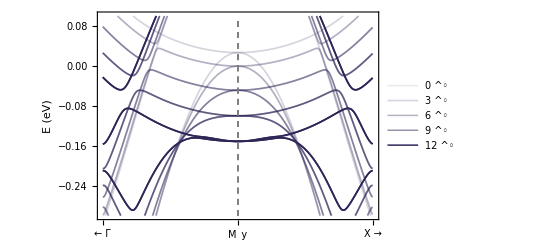

```mathematica
SpaghettiPlot2=Show[BandPlotList2,ImageSize->Full]
```

## Loading and cleaning ARPES data

#### Loading the data

Finally we load the ARPES data:

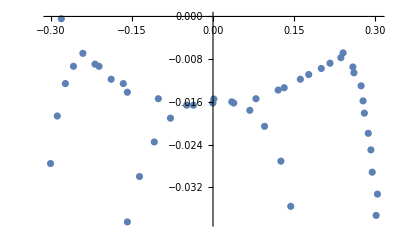

```mathematica
EData=Reverse[#]&/@Import[NotebookDirectory[]<>"/Surface_data_copy.txt","Table"(*,"FieldSeparators"->" ","LineSeparators"->","*)];
(*Reverse[#]&/@EData*)
ListPlot[EData]
```

### Cleaning the data

We have to do much to clean up the data and recast it in a format suitable for comparison to theory. We begin by attempting to decompose the data into distinct bands:

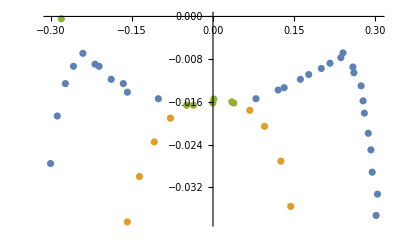

```mathematica
Band1={};
Band2={};
BandBad={};
Do[
If[Abs[kData[[1]]]>0.16&&kData[[2]]<-0.004,
AppendTo[Band1,kData]
,
If[-0.16<kData[[1]]<-0.06||0.16>kData[[1]]>0.04,
If[kData[[2]]<-0.017,
AppendTo[Band2,kData],
AppendTo[Band1,kData]
]
,
AppendTo[BandBad,kData];
]
]
,{kData,EData}]
ListPlot[{Band1,Band2,BandBad}]
```

Since it is not immediately clear if the green dots belong to upper or lower band, we put them into a separate list, before cleaning it up.

```mathematica
BandBad=SortBy[BandBad,First];
```

### Decomposing into distinct bands

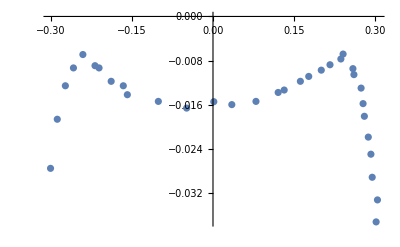

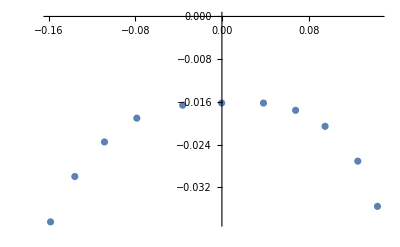

```mathematica
BandUp=SortBy[Join[Band1,{BandBad[[2]],BandBad[[5]],BandBad[[6]]}],First];
BandDown=SortBy[Join[Band2,BandBad[[3;;4]],{BandBad[[7]]}],First];
ListPlot[BandUp]
ListPlot[BandDown]
```

### Recasting ARPES data with full k-vectors (for comparison with theory)

Thus, we have decomposed the data into two distinct bands (up and down bands). We have to store this data into a list with the actual k vectors rather than k-lengths

```mathematica
BandPathData={};
Do[
CurData={};
If[kData[[1]]<0,
AppendTo[CurData,{0,π+3.869kData[[1]]}];
AppendTo[CurData,{kData[[2]]}];
AppendTo[CurData,{7}];
AppendTo[BandPathData,CurData];
,
AppendTo[CurData,{3.869kData[[1]],π}];
AppendTo[CurData,{kData[[2]]}];
AppendTo[CurData,{7}];
AppendTo[BandPathData,CurData];

];
,{kData,Band1(*Change to BandUp if needed*)}]

Do[
CurData={};
If[kData[[1]]<0,
AppendTo[CurData,{0,π+3.869kData[[1]]}];
AppendTo[CurData,{kData[[2]]}];
AppendTo[CurData,{6}];
AppendTo[BandPathData,CurData];
,
AppendTo[CurData,{3.869kData[[1]],π}];
AppendTo[CurData,{kData[[2]]}];
AppendTo[CurData,{6}];
AppendTo[BandPathData,CurData];
];
,{kData,Band2(*Change to BandDown if necessary*)}]
BandPathData;
```

## A function to tune and fit the band structure (Evaluate before proceeding further!)

This function requires significant improvements to make it suitable for general purpose use. For this reason we have not included it in the current version of BandUtilities.

```mathematica
TuneBandStructure[Hamltn_,SpaceDim_,ParamDim_,ParamRange_,NoPts_,BandPath_]:=
Module[{file1,file2,file3,file4,strm1,strm2,strm3,strm4,kVec,kVecFull,tVec,HamltnDim,InitSpace,ind,ValidData,MaxNoBands},
If[IntegerQ[SpaceDim]&&SpaceDim>0&&IntegerQ[ParamDim]&&ParamDim>0&&Length[ParamRange]==ParamDim&&Length[NoPts]==ParamDim&&AllTrue[ParamRange,Length[#]==2&&#[[1]]<#[[2]]&]&&AllTrue[NoPts,Length[#]==0&&#>0&&IntegerQ[#]&]&&Length[BandPath]>0&&
AllTrue[BandPath,Length[#]==3&&Length[#[[1]]]==SpaceDim&&Length[#[[2]]]==Length[#[[3]]]&],

HamltnDim=Length[Hamltn[ConstantArray[0,SpaceDim+ParamDim]]];
ValidData=False;
Do[
If[Length[kData[[2]]]==0&&NumberQ[kData[[2]]]&&IntegerQ[kData[[3]]]&&0<kData[[3]]<=HamltnDim,
(*kData[[1]] is the k-point. Here we check if there is only one energy to fit, given in kData[[2]], and if so, we further check if a valid band is provided in kData[[3]] whose band energy we shall try and fit.*)
ValidData=True;
,

If[AllTrue[kData[[2]],NumberQ[#]&]&&AllTrue[kData[[3]],IntegerQ[#]&&0<#<=HamltnDim&],
ValidData=True;
]
(*Checking if each element of kData[[2]] is a real number, i.e an energy, and each element of kData[[3]] is a valid band.*)
];
,{kData,BandPath}];

If[ValidData==True,
Print["Correct data format!"];

MaxNoBands=1;
Do[
If[Length[kData[[2]]]>MaxNoBands,
MaxNoBands=Length[kData[[2]]];
]
,{kData,BandPath}];

Print["Max number of bands = ",MaxNoBands];

file1=NotebookDirectory[]<>"cpp/HamltnTune.cpp";

strm1=OpenWrite[file1];

file2=NotebookDirectory[]<>"cpp/ParamLoops.cpp";

strm2=OpenWrite[file2];

file3=NotebookDirectory[]<>"cpp/kPath.cpp";

strm3=OpenWrite[file3];

file4=NotebookDirectory[]<>"cpp/PathLoop.cpp";

strm4=OpenWrite[file4];


kVec=Table[Symbol["k"<>ToString[i]],{i,1,SpaceDim}];
tVec=Table[Symbol["t"<>ToString[i]],{i,1,ParamDim}];

kVecFull=Join[kVec,tVec];


(*We begin by writing the Hamiltonian in HamltnTune.cpp*)
WriteString[strm1,"const int hmlt_dim = "<>ToString[HamltnDim]<>";\n"];
WriteString[strm1,"const int param_dim = "<>ToString[ParamDim]<>";\n\n"];

WriteString[strm1,"void hmlt_def(complex<double> **hmlt"];

Do[
WriteString[strm1,", double "<>ToString[ki]];
,{ki,kVecFull}];

WriteString[strm1,")\n"];

WriteString[strm1,"{\n"];

Do[
Do[
WriteString[strm1,"\t"<>"hmlt["<>ToString[i-1]<>"]["<>ToString[j-1]<>"] = "];

WriteString[strm1,StringDelete[ToString[CForm[Simplify[Hamltn[kVecFull][[i,j]]]//N]],"\n"|"\r"]];

WriteString[strm1,";\n"]
,{j,i,HamltnDim}]
,{i,1,HamltnDim}];

WriteString[strm1,"\n\n"];

Do[
Do[
WriteString[strm1,"\t"<>"hmlt["<>ToString[i-1]<>"]["<>ToString[j-1]<>"] = conj("<>"hmlt["<>ToString[j-1]<>"]["<>ToString[i-1]<>"]);\n"];
,{j,1,i-1}];
,{i,2,HamltnDim}];

WriteString[strm1,"}"];
Close[strm1];


(*We now proceed to write ParamLoops.cpp*)
InitSpace=""; (*This variable will be used for the purpose of aligning the code lines appropriately*)

WriteString[strm2,"#include \"kPath.cpp\"\n"];

WriteString[strm2,"\n"<>"int no_k_pts = "<>ToString[Length[BandPath]]<>";\n\n"];

WriteString[strm2,"double k1"];

Do[
WriteString[strm2,", k"<>ToString[n]];
,{n,2,SpaceDim}];

WriteString[strm2,";\n"];


WriteString[strm2,"double t1"];

Do[
WriteString[strm2,", t"<>ToString[n]];
,{n,2,ParamDim}];

WriteString[strm2,";\n\n"];

WriteString[strm2,"int grid_pts["<>ToString[ParamDim]<>"] = {"<>ToString[NoPts[[1]]]];

Do[
WriteString[strm2,", "<>ToString[NoPts[[i]]]];
,{i,2,ParamDim}];
WriteString[strm2,"};\n\n"];

WriteString[strm2,"double tmin["<>ToString[ParamDim]<>"] = {"<>ToString[ParamRange[[1,1]]//N]];

Do[
WriteString[strm2,", "<>ToString[ParamRange[[i,1]]//N]];
,{i,2,ParamDim}];
WriteString[strm2,"};\n"];

WriteString[strm2,"double tmax["<>ToString[ParamDim]<>"] = {"<>ToString[ParamRange[[1,2]]//N]];

Do[
WriteString[strm2,", "<>ToString[ParamRange[[i,2]]//N]];
,{i,2,ParamDim}];
WriteString[strm2,"};\n"];
WriteString[strm2,"double t_soln["<>ToString[ParamDim]<>"];\n\n"];

WriteString[strm2,"double Z_min, Z_soln, b_min, b_soln, A_sum, B_sum, Asqr_sum, Bsqr_sum, AB_sum, Z_numer, Z_denom, err, err_soln;\n"<>"err_soln = 1.5e8;\n\n"];

(*The following code will write the loops that will be used to traverse the range of parameters:*)

Do[
WriteString[strm2,InitSpace<>"for(int i"<>ToString[n]<>" = 0; i"<>ToString[n]<>" < grid_pts["<>ToString[n-1]<>"]; i"<>ToString[n]<>"++)\n"];

WriteString[strm2,InitSpace<>"{\n"];

InitSpace=InitSpace<>"\t";

WriteString[strm2,InitSpace<>"t"<>ToString[n]<>" = tmin["<>ToString[n-1]<>"] + (1. * i"<>ToString[n]<>" / grid_pts["<>ToString[n-1]<>"]) * (tmax["<>ToString[n-1]<>"] - tmin["<>ToString[n-1]<>"]);\n\n"];
,{n,1,ParamDim}];

WriteString[strm2,InitSpace<>"Z_numer = 0.;\n"<>InitSpace<>"Z_denom = 0.;\n"<>InitSpace<>"Z_min = 1.;\n"<>InitSpace<>"err = 0.;\n"<>InitSpace<>"A_sum = 0.;\n"<>InitSpace<>"B_sum = 0.;\n"<>InitSpace<>"AB_sum = 0.;\n"<>InitSpace<>"Bsqr_sum = 0.;\n"<>InitSpace<>"Asqr_sum = 0.;\n\n"];

WriteString[strm2,InitSpace<>"#include \"PathLoop.cpp\"\n\n"];

WriteString[strm2,InitSpace<>"if(err < err_soln)\n"<>InitSpace<>"{\n"];
WriteString[strm2,InitSpace<>"\t"<>"found = true;\n"];
WriteString[strm2,InitSpace<>"\t"<>"err_soln = err;\n"];
WriteString[strm2,InitSpace<>"\t"<>"Z_soln = Z_min;\n"<>InitSpace<>"\t"<>"b_soln = b_min;"];
Do[
WriteString[strm2,InitSpace<>"\n"<>InitSpace<>"\t"<>"t_soln["<>ToString[i-1]<>"] = t"<>ToString[i]<>";"];
,{i,1,ParamDim}];
WriteString[strm2,"\n"<>InitSpace<>"}\n"];

Do[
InitSpace=StringReplace[InitSpace,"\t"->"",1];
WriteString[strm2,InitSpace<>"}\n"];
,{i,1,ParamDim}];

Close[strm2];


(*Now we write kPath.cpp which contains the k-path as a multidimensional array*)

WriteString[strm3,"double kPath["<>ToString[Length[BandPath]]<>"]["<>ToString[SpaceDim+1+2MaxNoBands]<>"] = {"];

ind=1;
Do[
WriteString[strm3,ToString[Join[kp[[1]]//N,{Length[kp[[2]]]},kp[[2]]//N,(#-1)&/@kp[[3]],ConstantArray[-1,2(MaxNoBands-Length[kp[[2]]])]]]];

If[ind<Length[BandPath],
ind++;
WriteString[strm3,","];
]
,{kp,BandPath}];

WriteString[strm3,"};"];


Close[strm3];


(*Finally, we write the loop over the k-path in PathLoop.cpp*)
WriteString[strm4,"int no_E_pts, no_bands;\n"<>"no_E_pts = 0;\n\n"];

WriteString[strm4,"for(int l = 0; l < no_k_pts; l++)\n{\n"];

Do[
WriteString[strm4,"\t"<>"k"<>ToString[i]<>" = kPath[l]["<>ToString[i-1]<>"];\n"]
,{i,1,SpaceDim}];

WriteString[strm4,"\n\t"<>"hmlt_def(hmlt"];
Do[
WriteString[strm4,", "<>ToString[ki]];
,{ki,kVecFull}];
WriteString[strm4,");\n"];

WriteString[strm4,"\t"<>"zheev(hmlt, hmlt_dim, evals);\n\n"];

(*
Do[
WriteString[strm4,"\t"<>"kPath[l]["<>ToString[i-1+SpaceDim+Length[Bands]]<>"] = evals["<>ToString[Bands[[i]]-1]<>"];\n"];
,{i,1,Length[Bands]}];
*)

WriteString[strm4,"\n\t"<>"no_bands = (int) kPath[l]["<>ToString[SpaceDim]<>"];\n"];
(*The first SpaceDim elements of kPath[l] are the k values. The next contains the number of energies/bands invloved in the fitting. The next is the set of energies and then finally the band indices.*)

WriteString[strm4,"\n\t"<>"no_E_pts += no_bands;\n"];

WriteString[strm4,"\n\t"<>"for(int j = 0; j < no_bands; j++)\n\t{\n"];

WriteString[strm4,"\n\t\t"<>"AB_sum += kPath[l]["<>ToString[SpaceDim+1]<>" + j] * evals[(int)(kPath[l]["<>ToString[SpaceDim+1]<>" + no_bands + j])];\n"];


WriteString[strm4,"\n\t\t"<>"A_sum += kPath[l]["<>ToString[SpaceDim+1]<>" + j];\n"];


WriteString[strm4,"\n\t\t"<>"B_sum += evals[(int)(kPath[l]["<>ToString[SpaceDim+1]<>" + no_bands + j])];\n"];

WriteString[strm4,"\n\t\t"<>"Asqr_sum += kPath[l]["<>ToString[SpaceDim+1]<>" + j] * kPath[l]["<>ToString[SpaceDim+1]<>" + j];\n"];


WriteString[strm4,"\n\t\t"<>"Bsqr_sum += evals[(int)(kPath[l]["<>ToString[SpaceDim+1]<>" + no_bands + j])] * evals[(int)(kPath[l]["<>ToString[SpaceDim+1]<>" + no_bands + j])];\n"];

WriteString[strm4,"\n\t}\n}"];

WriteString[strm4,"\n\n"<>"Z_numer = AB_sum - A_sum * B_sum / (1. * no_E_pts);"];
WriteString[strm4,"\n"<>"Z_denom = Bsqr_sum - B_sum * B_sum / (1. * no_E_pts);"];


WriteString[strm4,"\n\n"<>"if(Z_denom == 0 || (Z_numer * Z_denom) < 0)\n{\n\t"<>"cout<<\"\\n Z factor denominator vanished at iteration TODO!\\n\";"(*<>"\n\t"<>"continue;\n}\n"*)<>"\n}\n"<>"else\n{\n\t"<>"Z_min = Z_numer / Z_denom;\n\t"<>"b_min = (Z_min * B_sum - A_sum)/(1. * no_k_pts);\n}\n\n"];

WriteString[strm4,"err = Asqr_sum + Z_min * Z_min * Bsqr_sum + 2. * b_min * (A_sum - Z_min * B_sum) - 2. * Z_min * AB_sum + b_min * b_min * no_E_pts;"];

Close[strm4];

Print["Done!!"];

,
Print[Style["Incorrect format for BandPath. BandPath should contain a list of k-points along with the energies and the bands to fit to these energies. (For example, an element of BandPath has the format {{k_1,k_2,...,k_SpaceDim},{E_1,E_2,...,E_M},{band_1,band_2,...,band_M}}, where E_i are real and band_i are positive integers between 1 and HamltnDim.)",Red]]
]
,
Print[Style["Invalid input parameters! Call the function as TuneBandStructure[Hamltn, SpaceDim, ParamDim, ParamRange, NoPts, BandPath], with a valid Hamiltonian Hamltn, positive integer SpaceDim and ParamDim, and lists ParamRange and NoPts respectively having the form {{t_1^min,t_1^max},{t_2^min,t_2^max},...,{t_ParamDim^min,t_ParamDim^max}} and {N_1,N_2,...,N_ParamDim}, with t_i^min<t_i^max and positive integer N_i for 1 ≤ i ≤ ParamDim (i.e the number of parameters is ParamDim). And BandPath should contain a list of k-points along with the energies and the bands to fit to these energies. (For example, an element of BandPath has the format {{k_1,k_2,...,k_SpaceDim},{E_1,E_2,...,E_M},{band_1,band_2,...,band_M}}, where E_i are real and band_i are positive integers between 1 and HamltnDim).",Red]]
]
]
```

## Fitting the ARPES data

```mathematica
TuneBandStructure[HamSOC,2,2,{{0,12},{0.01,0.4}},{130,50},BandPathData]
```

Correct data format!

Max number of bands = 1

Done!!

We will still have to compile and run the cpp program

```mathematica
Print["Run the following commands on Linux terminal in sequence:\n","cd "<>NotebookDirectory[]<>"cpp/ \n","g++ Tune.cpp -o Tune -llapack -lblas -fopenmp \n","./Tune"];
```

Run the following commands on Linux terminal in sequence:
cd /Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/cpp/ 
g++ Tune.cpp -o Tune -llapack -lblas -fopenmp 
./Tune

If you use a Mac, things can get a bit complicated since the native support for OpenMP was disabled some time back. I used XCode and then Homebrew to install and link it. In that situation, the library and include directories have to be found and included. For example, I used the following

```mathematica
Print["Instead run the following commands on a Mac terminal:\n","cd "<>NotebookDirectory[]<>"cpp/ \n","clang++ Tune.cpp -o Tune -llapack -lblas -Xclang -fopenmp -lomp -L/opt/homebrew/opt/libomp/lib -I/opt/homebrew/opt/libomp/include \n","./Tune"];
```

Instead run the following commands on a Mac terminal:
cd /Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/cpp/ 
clang++ Tune.cpp -o Tune -llapack -lblas -Xclang -fopenmp -lomp -L/opt/homebrew/opt/libomp/lib -I/opt/homebrew/opt/libomp/include 
./Tune

After running the program we can read its output

```mathematica
{θFit,λFit,ZFit,E0Fit,ErrFit}=Import[NotebookDirectory[]<>"cpp/TuningSolution.dat"][[1]];
Print["Best fit parameters: θ = ",θFit,", λ_SOC = ",λFit,", Z = ",ZFit,", E_F = ",E0Fit", % Error = ",100ErrFit];
```

Best fit parameters: θ = 8.03077, λ_SOC = 0.1738, Z = 0.244404, E_F = -0.00262535 , % Error = 0.0139292

Using this, we define a number of Hamiltonians to be used for different purposes

```mathematica
HamFit[k_]:=ZFit Hamiltonian[k[[1]]-k[[2]],k[[1]]+k[[2]],θFit,λFit]- DiagonalMatrix[ConstantArray[E0Fit,12]]
HamFitNoSOC[k_]:=ZFit Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θFit]- DiagonalMatrix[ConstantArray[E0Fit,6]]
HamTuneNoSOC[k_]:=ZFit Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]]]- DiagonalMatrix[ConstantArray[E0Fit,6]]
HamTuneNoSOCmeV[k_]:=1000ZFit Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]]]- 1000DiagonalMatrix[ConstantArray[E0Fit,6]]
HamTuneSOCmeV[k_]:=1000ZFit Hamiltonian[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],λFit]- 1000DiagonalMatrix[ConstantArray[E0Fit,12]]
HamFullTuneSOCmeV[k_]:=1000ZFit Hamiltonian[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],k[[4]]]- 1000DiagonalMatrix[ConstantArray[E0Fit,12]]
```

## Comparing ARPES bands with the bands from the best - fit Hamiltonian - first pass

### Generating the band-structure data to plot

```mathematica
HamFitmeV[k_]:=1000HamFit[k];
Bnd1=GenerateBandStructure[HamFitmeV,HSymmPts2];
```

### Plotting the best fit band-structure and ARPES data together for comparison

Finally we plot the band of the theory fit Hamiltonian along with the experimental data in meV:

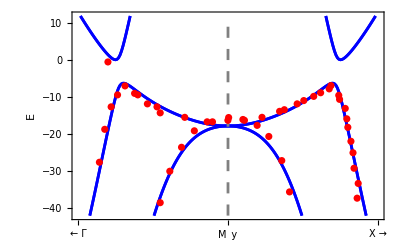

```mathematica
plt1=PlotBandStructure[Bnd1,(*{-0.042,0.012}*){-42,12},"AspectRatio"->3/5];
plt2=ListPlot[({3.869(#[[1]]+0.35),1000#[[2]]})&/@EData,PlotStyle->Red];
Show[plt1,plt2]
```

### Writing the interpolated Wannier90 data

Time to write the interpolated Hamiltonian into Wannier90 format, with and without the SOC term:

```mathematica
WriteTBM[NotebookDirectory[]<>"output_models/Sr2RuO4_8p03degrees_SOC_hr.dat",W90Data[[2]],"ParameterValue"->θFit,"ParameterSymbol"->"θ","BandRenormalization"->ZFit,"FermiLevel"->E0Fit,"SpinOrbitMatrix"->λFit HSOC];

WriteTBM[NotebookDirectory[]<>"output_models/Sr2RuO4_8p03degrees_noSOC_hr.dat",W90Data[[2]],"ParameterValue"->θFit,"ParameterSymbol"->"θ","BandRenormalization"->ZFit,"FermiLevel"->E0Fit];
```

Valid SOC matrix provided. Doubling the number of orbitals and writing the Wannier90 data.

Invalid or no SOC matrix provided! Writing an SOC-free Hamiltonian.

### Sanity Checks

We load the saved Wannier tight binding model and check if it reproduces the ARPES comparison figure

```mathematica
Hamiltonian2[k1_,k2_]=LoadTBM[NotebookDirectory[]<>"output_models/Sr2RuO4_8p03degrees_SOC_hr.dat","FileType"->"Wannier90"][[1]];
```

Invalid or no lattice vectors provided! Using unit vectors.

Wannier data begins at line 10.

Tight-binding data file loaded.

Space dimension: 3

Number of orbitals: 12

Number of supercells: 79

First row of data: {-4,-3,0,1,1,0.,0.}

Last row of data: {4,3,0,12,12,0.,0.}

Number of entries: 11376

Loading Hamiltonian.

No valid symmetrization scheme provided! We will not symmetrize the loaded Hamiltonian.

Using this we define another Hamiltonian to be used exclusively for plotting the band

```mathematica
HamFitmeV2[k_]:=1000Hamiltonian2[k[[1]]-k[[2]],k[[1]]+k[[2]]];
Bnd2=GenerateBandStructure[HamFitmeV2,HSymmPts2];
```

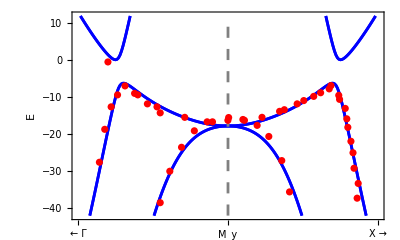

```mathematica
plt3=PlotBandStructure[Bnd2,(*{-0.042,0.012}*){-42,12},"AspectRatio"->3/5];
Show[plt3,plt2]
```

Thus we have verified that it neatly reproduces the original comparison.

## The Fermi surface

We will use brute force to calculate the Fermi surface. The functions to do this also need significant improvements to improve their useability and have therefore not been included in the library

### Extra function (execute this before proceeding further)

```mathematica
(*A brute force method to calculate Fermi surface. Needs to be rewritten/improved to incorporate better method of calculating the Fermi surface.*)
GenerateFermiSurfaceData[FermiLevel_,SpaceDim_,BZ_,Resln_:0.5 10^-3,Grid_:-1]:=
Module[{file1,file2,prog,strm,GridPts,valid,txt},

If[IntegerQ[SpaceDim]&&SpaceDim>0,
(*If the k-space dimension is a positive integer.*)

If[Grid==-1||(Length[Grid]!=SpaceDim&&Length[Grid]!=0),
(*This means that either no grid mesh is provided, or an invalid one is given*)
GridPts=ConstantArray[1000,SpaceDim];

txt="1000";
Do[txt=txt<>"x1000";,
{j,2,SpaceDim}];

Print[Style["Invalid grid or no grid provided! Using a "<>txt<>" grid of k points."]];
,
If[Length[Grid]==0&&IntegerQ[Grid]&&Grid>0,
(*If a single positive integer is provided, we use a hypercubic grid with (Grid x Grid x....x Grid) k-points.*)
GridPts=ConstantArray[Grid,SpaceDim];
,
If[Length[Grid]=SpaceDim&&AllTrue[Grid,IntegerQ[#]&&#>0&],
(*If instead Grid is an array having same dimension as the k-space, we check if all its elements are positive integers, in which case it is a valid grid.*)
GridPts=Grid;
,
GridPts=ConstantArray[1000,SpaceDim];

txt="1000";
Do[txt=txt<>"x1000";,
{j,2,SpaceDim}];

Print[Style["Invalid grid provided! Using a "<>txt<>" grid of k points."]];

]
]
];

If[ArrayDepth[BZ]==2&&Length[BZ]==SpaceDim&&AllTrue[Flatten[BZ],NumericQ]&&AllTrue[BZ,Length[#]==2&&#[[1]]<#[[2]]&],
(*We are checking above if
1. BZ is a two dimensional array.
2. Number of sublists within it is equal to SpaceDim,
3. Each sublist has exactly two elements, both of which are numbers.
4. The numbers in each sublist are properly ordered as Subscript[k, i]^min,Subscript[k, i]^max.
*)
file1=NotebookDirectory[]<>"cpp/params.dat";

file2=NotebookDirectory[]<>"cpp/FS.dat";

strm=OpenWrite[file1];

Do[
WriteString[strm,ToString[N[BZ[[i,1]]]]<>" "<>ToString[N[BZ[[i,2]]]]<>"\n"];
,{i,1,SpaceDim}];

Do[
WriteString[strm,ToString[GridPts[[i]]]<>"\n"];
,{i,1,SpaceDim}];

WriteString[strm,ToString[FermiLevel]<>"\n"];

WriteString[strm,ToString[Resln]<>"\n"];

WriteString[strm,ToString[file2]];

Close[strm];

valid=-1;

prog="(cd "<>NotebookDirectory[]<>"cpp/ ; ./FermiSurface)";

Print["Now going to run "<>prog];

valid=Run[prog];

If[valid!=0,
Print[Style["Runtime failiure! Try running the function WriteHamiltonian[Ham_,SpaceDim_] with a legitimitate Hamiltonian and correct k-space dimension first, and then re-run this function with the same SpaceDim. Alternatively, check if the C++ files are stored in the local folder named cpp.",Red]]
,
OpenRead[NotebookDirectory[]<>"cpp/FS.dat"]
]
,

Print[Style["Invalid region provided! It has to be given as a list having the form {{k_1^min,k_1^max},{k_2^min,k_2^max},...,{k_n^min,k_n^max}}",Red]]
]
,
Print[Style["Invalid k-space dimension! It has to be an integer greater than or equal to 1.",Red]]
]
]
```

### Generating the Fermi surface

Firstly we write the Hamiltonian to a C++ file

```mathematica
WriteHamiltonianCPP[HamFit,2]
```

Invalid or no file path provided! Reverting to the default name Hamltn.cpp. File shall be stored in the directory cpp located in the local directory of the notebook.

Hamiltonian successfully written to Hamltn.cpp. Please include both Hamltn.cpp and ancillaries.cpp in your code.

Before running the routine to generate the Fermi surface, compile FermiSurface.cpp with flags -llapack and -lblas. The file is located in the cpp folder.

```mathematica
GenerateFermiSurfaceData[0.,2,{{-π,π},{-π,π}}]
```

Invalid grid or no grid provided! Using a 1000x1000 grid of k points.

Now going to run (cd /Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/cpp/ ; ./FermiSurface)

InputStream[…]

### Plotting the Fermi surface

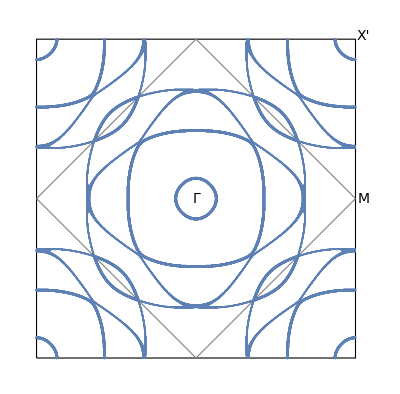

/Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/Fermi_Surface.pdf

```mathematica
file3=NotebookDirectory[]<>"cpp/FS.dat";
(*Close[strm3]*)
strm3=OpenRead[file3];

F3=Read[strm3];
Close[strm3];
FermiList3=First@Last@Reap[Do[If[Length[band]!=0,Sow[ListPlot[band[[All,1]],AspectRatio->1,Axes->False,Ticks->None,Frame->True,FrameTicks->None,PlotRange->{{-π,π},{-π,π}}]]],{band,F3}]];
pltFS=Show[Graphics[Text[Style["Γ",FontSize->14,FontFamily->"Times"],{0,0}]],Graphics[Text[Style[" X'",FontSize->14,FontFamily->"Times"],{1.05π,1.02π}]],Graphics[Text[Style["  M",FontSize->14,FontFamily->"Times"],{1.05π,0}]],Graphics[{EdgeForm[{Black}],FaceForm[],Rectangle[{-π,-π},{π,π}]}],Graphics[{EdgeForm[{Gray,Dashed}],FaceForm[],Polygon[{{-π,0},{0,π},{π,0},{0,-π}}]}],FermiList3]

Export[NotebookDirectory[]<>"Fermi_Surface.pdf",Show[pltFS,ImageSize->7 cm]]
```

Loading the experimental Fermi surface below (sourced from Fig 7 of Phys. Rev. X 9, 021048, https://journals.aps.org/prx/abstract/10.1103/PhysRevX.9.021048 ), for comparison:

```mathematica
Import[NotebookDirectory[]<>"Fermi_Surface_expt.png"]
```

-Graphics-

For a more careful comparison check FIG. 3 of our paper: https://arxiv.org/pdf/2310.15331